# First Plot

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw=Import["modelFit.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]]
```

{A_M_Pred,A_Av_M_Obs,A_F_Pred,A_Av_F_Obs,B_M_Pred,B_Av_M_Obs,B_F_Pred,B_Av_F_Obs,C_M_Pred,C_Av_M_Obs,C_F_Pred,C_Av_F_Obs,D_M_Pred,D_Av_M_Obs,D_F_Pred,D_Av_F_Obs}

{{0.047619,0.047619,0,0,0.2,0.2,0,0,0.333333,0.333333,0,0,0.5,0.5,0,0},{0.086,0.08476,0,0.00025,0.315333,0.270208,0,0.00152934,0.473,0.401054,0,0.00367502,0.946,0.549596,0,0.0166616},{0.08132,0.122258,0.0000360494,0.00102083,0.297658,0.31739,0.000647006,0.00394758,0.445567,0.435863,0.0018913,0.0126913,0.821085,0.569134,0.0738306,0.0309902},{0.076834,0.15229,0.0000675945,0.0034745,0.279815,0.327272,0.00129495,0.0144152,0.416118,0.424509,0.00404437,0.027417,0.610408,0.451269,0.147409,0.0544324},{0.0725425,0.197691,0.0000948074,0.00727579,0.262111,0.334421,0.00191787,0.0211839,0.385964,0.367229,0.00631112,0.038692,0.49903,0.384477,0.169296,0.0706009},{0.0684431,0.214025,0.000117984,0.0104468,0.244687,0.314694,0.00249915,0.0309273,0.355613,0.331076,0.00856435,0.0399378,0.407921,0.442187,0.175854,0.0820593},{0.064533,0.181537,0.000137429,0.0200168,0.227691,0.285798,0.00302505,0.0373203,0.325734,0.296654,0.0106815,0.0418002,0.340718,0.434656,0.171659,0.130763},{0.0608084,0.2112,0.000153452,0.0221861,0.21126,0.333349,0.00348536,0.0450509,0.296907,0.303426,0.0125641,0.0658841,0.289592,0.481508,0.16324,0.189022},{0.0572654,0.217405,0.000166361,0.0376065,0.195506,0.340555,0.00387376,0.0623628,0.2696,0.376694,0.0141472,0.103353,0.250173,0.477475,0.1533,0.156916}}

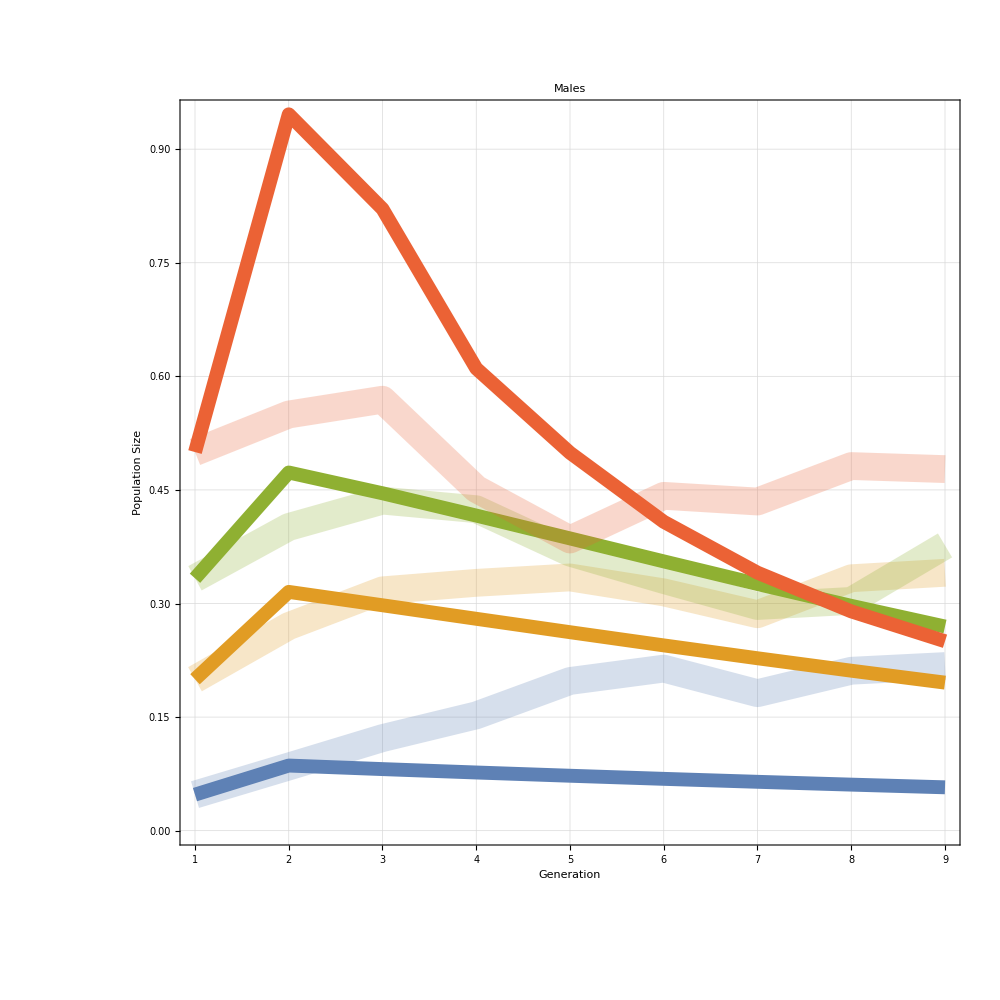
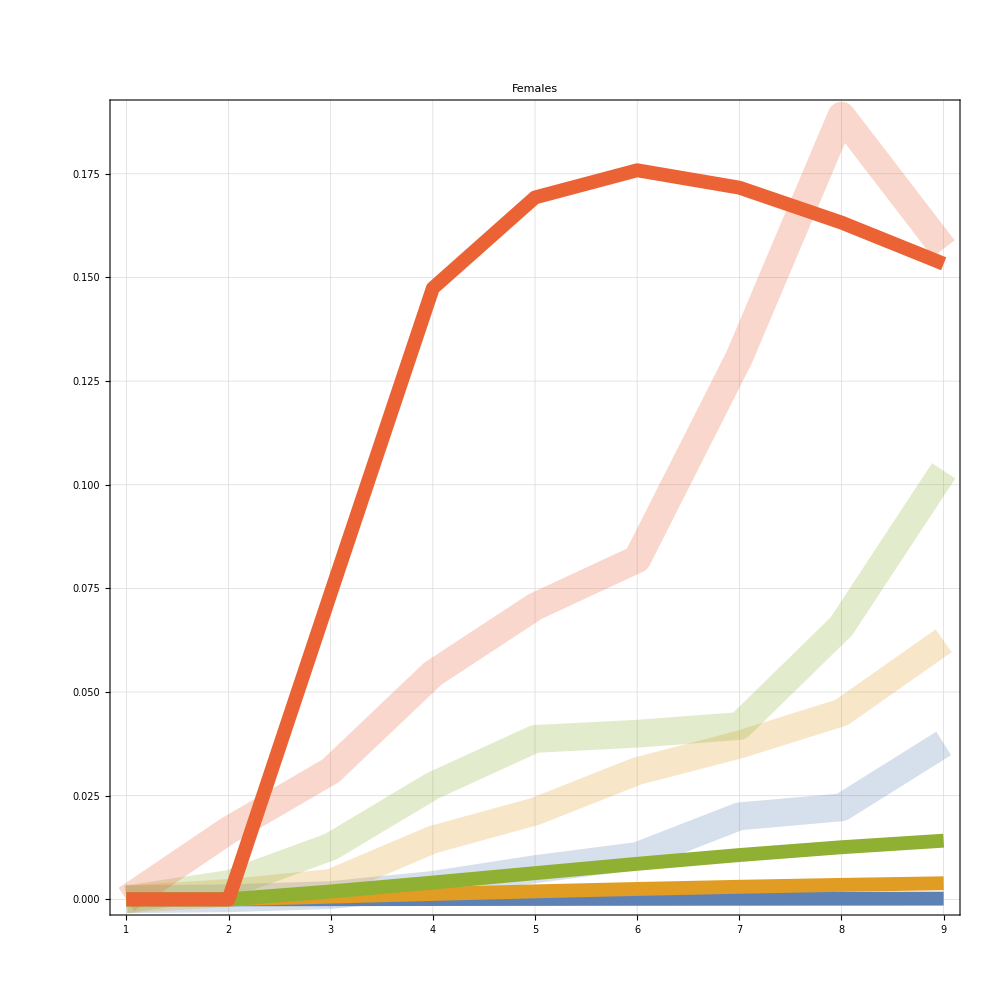
-Graphics- | -Graphics- |

experimentsGrid.pdf

```mathematica
plotOneIndices=Flatten[Position[labels,#]&/@{"A_M_Pred","A_Av_M_Obs","B_M_Pred","B_Av_M_Obs","C_M_Pred","C_Av_M_Obs","D_M_Pred","D_Av_M_Obs"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Generation","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Males",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"A_F_Pred","A_Av_F_Obs","B_F_Pred","B_Av_F_Obs","C_F_Pred","C_Av_F_Obs","D_F_Pred","D_Av_F_Obs"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Females",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;4]],{"1","2","3","4"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",30]
];
grid=Grid[{{males,females,swatch}}]
Export["experimentsGrid.pdf",grid]
```

# Second Plot

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw=Import["modelFit2.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]];
```

{D_Female_Pred,D_D_Allele_Pred,D_W_Allele_Pred,D_R_Allele_Pred,D_B_Allele_Pred,I_Female_Pred,I_D_Allele_Pred,I_W_Allele_Pred,I_R_Allele_Pred,I_B_Allele_Pred}

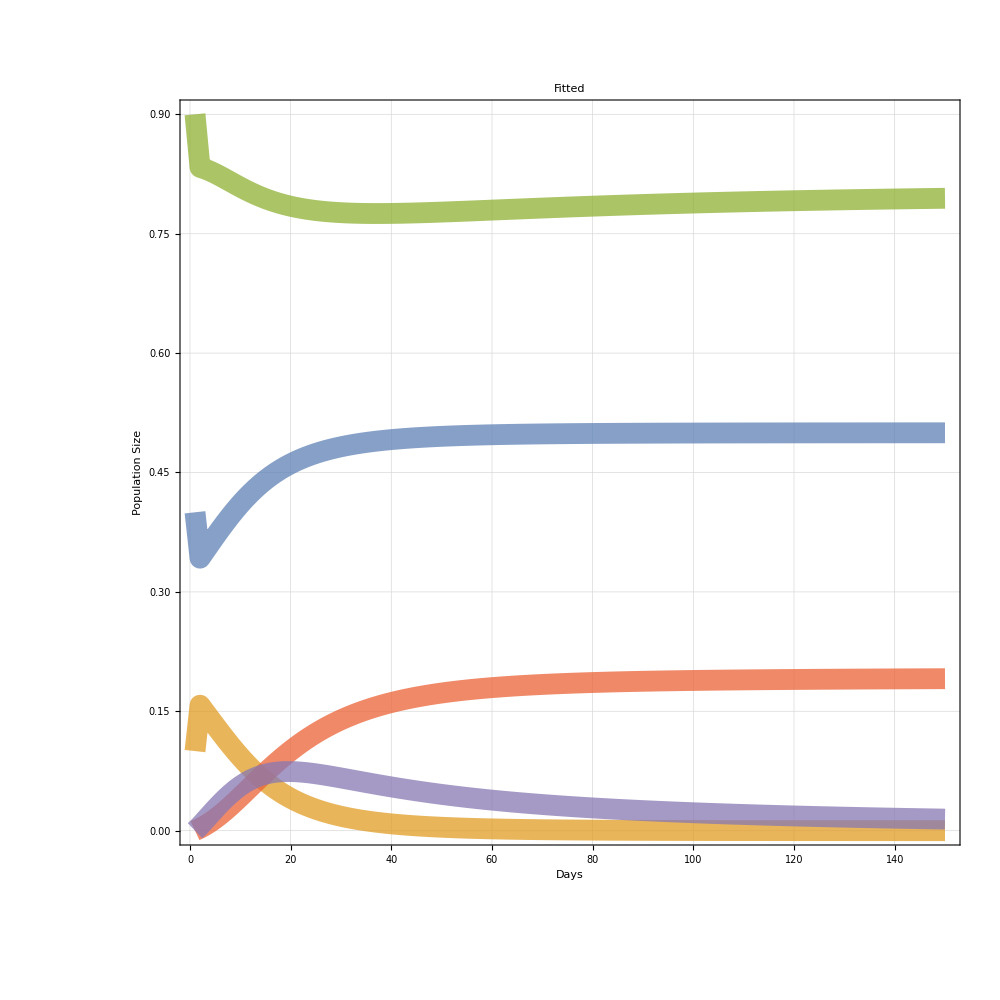
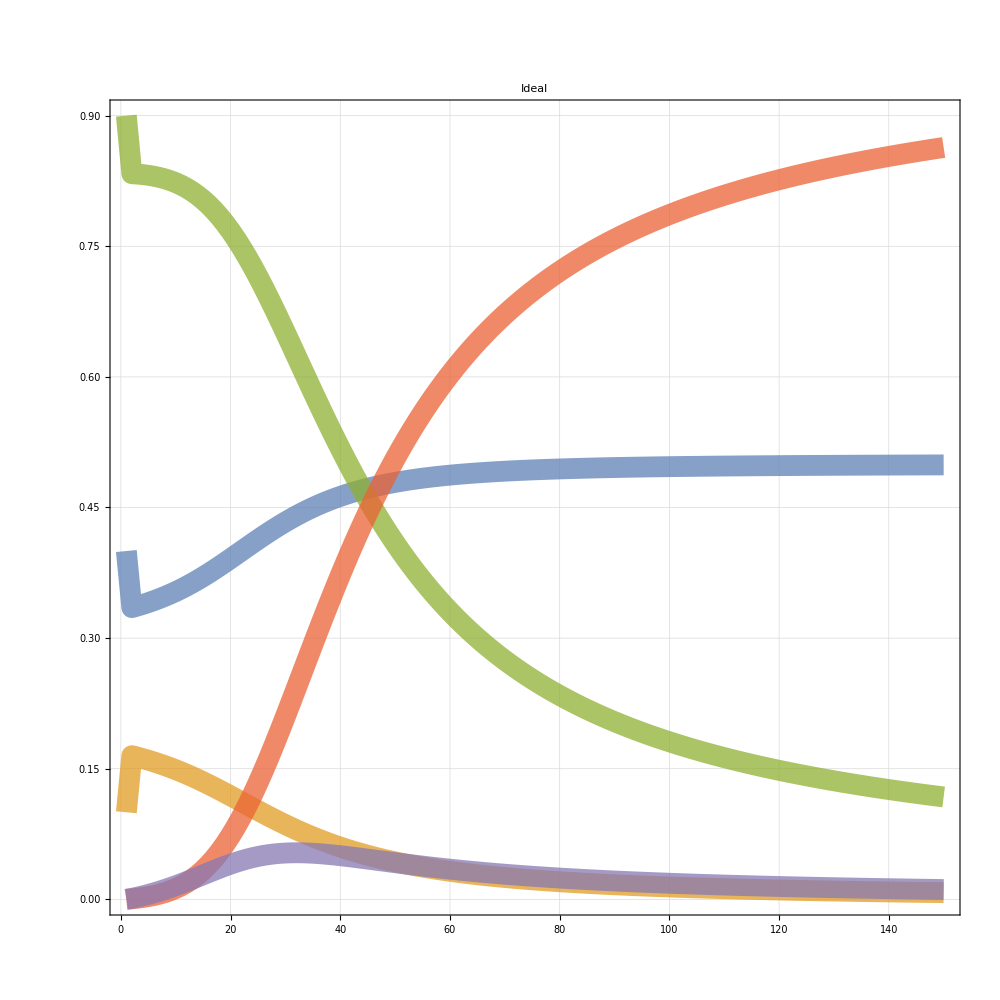
-Graphics- | -Graphics- |

experimentsGrid2.pdf

```mathematica
plotOneIndices=Flatten[Position[labels,#]&/@{"D_Female_Pred","D_D_Allele_Pred","D_W_Allele_Pred","D_R_Allele_Pred","D_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Days","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Fitted",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"I_Female_Pred","I_D_Allele_Pred","I_W_Allele_Pred","I_R_Allele_Pred","I_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Ideal",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;5]],{"B","D","XX","R","W"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",30]
];
grid=Grid[{{males,females,swatch}}]
Export["experimentsGrid2.pdf",grid]
```

# Third Plot

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/ModelFits

{90%,75%,50%,25%,10%}

{{0.9,0.855,0.777273,0.63888,0.485476,0.359363,0.264753,0.198423,0.151788,0.1186,0.0944834,0.0765705,0.0629829,0.0524757,0.0442091,0.0376047,0.032256,0.0278719,0.0242399,0.0212023,0.0186401,0.0164624,0.014599,0.0129945,0.0116052,0.0103962},{0.75,0.719697,0.658759,0.574238,0.474952,0.379969,0.298447,0.233849,0.184324,0.146818,0.118371,0.0966137,0.0797801,0.0665899,0.0561225,0.0477144,0.0408833,0.0352752,0.0306269,0.0267404,0.023465,0.0206846,0.0183088,0.0162666,0.0145015,0.0129683},{0.5,0.475,0.440244,0.400589,0.356567,0.31149,0.26799,0.228145,0.193037,0.16294,0.137592,0.116465,0.0989407,0.0844224,0.0723767,0.0623511,0.0539722,0.0469362,0.0409981,0.035961,0.0316667,0.0279875,0.0248205,0.0220821,0.0197042,0.017631},{0.25,0.316667,0.295902,0.273827,0.250575,0.226962,0.203703,0.181438,0.160645,0.141621,0.1245,0.109284,0.0958884,0.0841713,0.0739663,0.0651,0.0574051,0.0507265,0.0449254,0.0398794,0.0354822,0.0316424,0.0282815,0.0253328,0.0227394,0.0204528},{0.1,0.105556,0.0997238,0.093972,0.0883176,0.082795,0.0774342,0.0722614,0.0672981,0.0625613,0.0580629,0.0538103,0.0498069,0.046052,0.042542,0.0392707,0.0362297,0.0334093,0.0307984,0.0283855,0.0261587,0.0241059,0.0222154,0.0204755,0.0188752,0.0174039}}

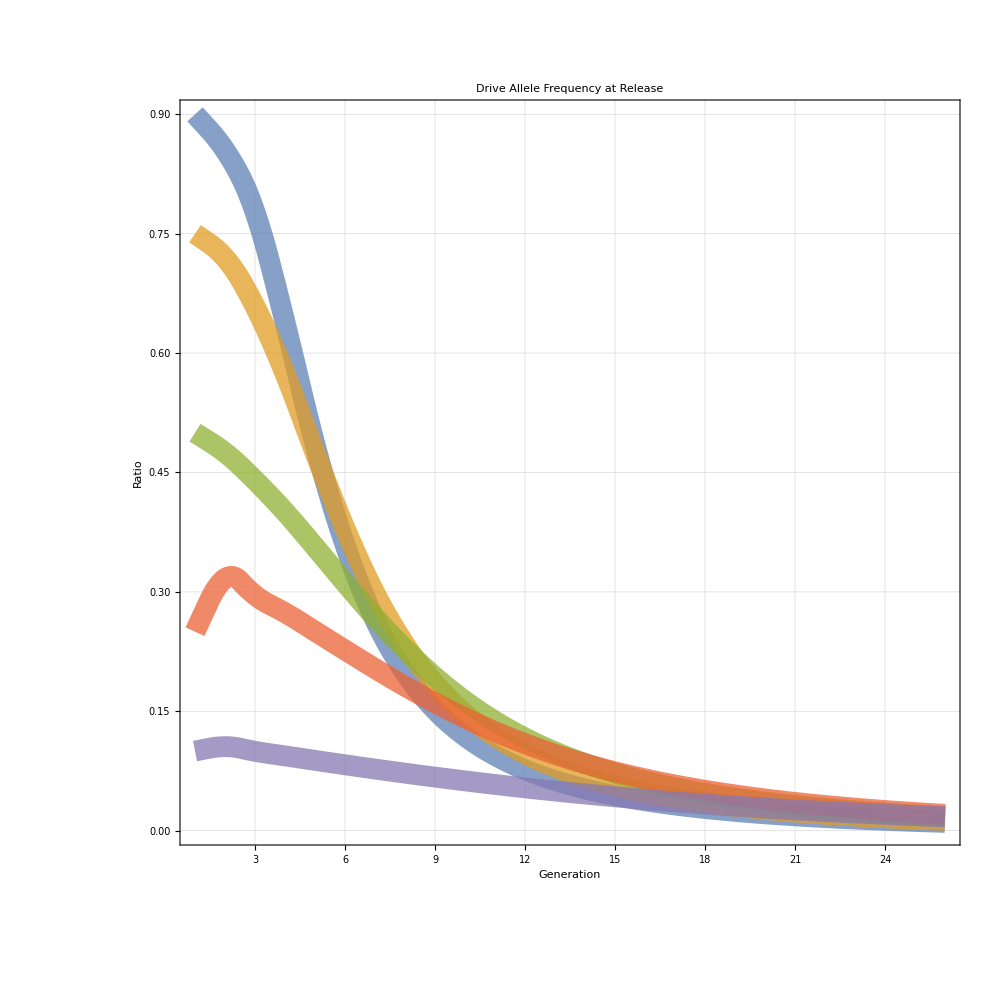
-Graphics- |

```mathematica
SetDirectory[NotebookDirectory[]]
rawData=Import["DMplot.csv"][[2;;All]];
dataTitle=rawData[[1,2;;All]]
data=rawData[[2;;All,2;;All]]//Transpose
plot=ListLinePlot[data,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[dataTitle]]])),
AspectRatio->1,
InterpolationOrder->2,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->40,
FrameLabel->(Style[#,Gray,60]&/@{"Generation","Ratio"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Drive Allele Frequency at Release",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;5]],dataTitle,
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["",30]
];
Grid[{{plot,swatch}}]
```